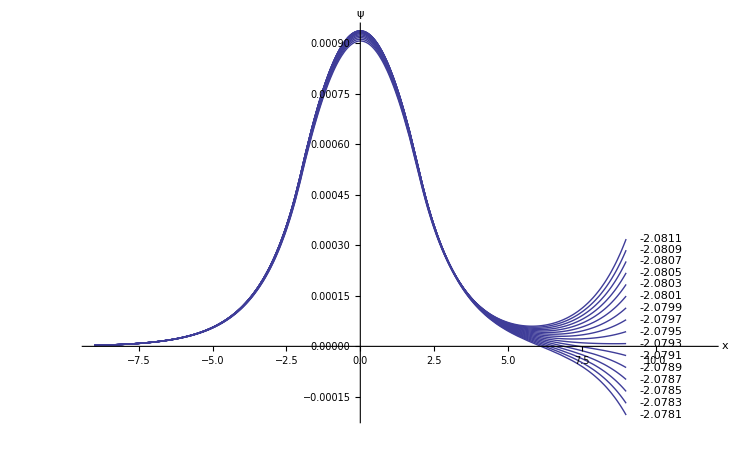

```mathematica
V0=3;a=2;α=0.262713;ψ0=1;
x0=4.5a;x1=-x0;x2=x0;
n=100;δ=0.02/n;
V[x_]:=Which[Abs[x]≤a,-V0,True,0]
data={};txt={};
Do[
equ={ψ''[x]+α(Ε-V[x])ψ[x]==0,ψ[x1]==ψ0,ψ'[x1]==√(-α(Ε-V[x1])) ψ0};
s=NDSolve[equ,ψ,{x,x1,x2}];
ϕ=ψ/.s[[1]];
total=NIntegrate[ϕ[x]^2,{x,x1,x2}];
g=Plot[ϕ[x]/total,{x,x1,x2},
PlotRange->{{x1,1.3x2},All}];
AppendTo[data,g];
AppendTo[txt,
Text[ToString[Ε],{1.13x2,ϕ[x2]/total}]],
{Ε,-2.0811,-2.078,δ}]
Show[data,Graphics[txt],
AxesOrigin->{0,0},AxesLabel->{"x","ψ"}]
Clear["Global`*"]
```